# Right Triangle

### Author

Eric W. Weisstein
July 31, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Triangles/RightTriangle.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/RightTriangle.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

### Definitions

```mathematica
ineq=y≥0&&a b≥b x+a y&&x≥0;
```

```mathematica
implreg=ImplicitRegion[ineq,{x,y}];
```

```mathematica
verts={{0,0},{a,0},{0,b}};
```

```mathematica
reg=Triangle[verts]
```

Triangle[{{0,0},{a,0},{0,b}}]

```mathematica
assum=a>0&&b>0;
```

```mathematica
t=FullSimplify[Triangle[𝒶,𝒷,Sqrt[𝒶^2+𝒷^2]],𝒶>0&&𝒷>0]
```

Triangle[{{0,0},{√(𝒶^2+𝒷^2),0},{𝒷^2/(√(𝒶^2+𝒷^2)),(𝒶 𝒷)/(√(𝒶^2+𝒷^2))}}]

```mathematica
abc=Simplify[SideLengths[Evaluate[t]],𝒶>0&&𝒷>0]
```

{𝒶,𝒷,√(𝒶^2+𝒷^2)}

## Plots

### Diagram

```mathematica
LaminaData["FilledRightTriangle","Diagram"]
```

-Graphics-

### DiscretizeRegion

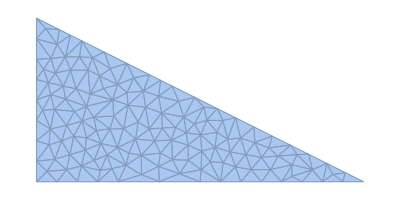
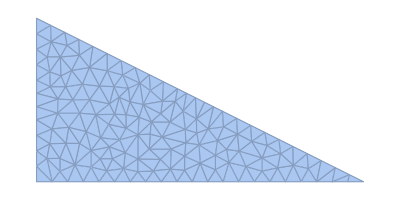

```mathematica
Block[{a=1,b=.5},DiscretizeRegion[#]]&/@{reg,implreg}
```

### RegionPlot

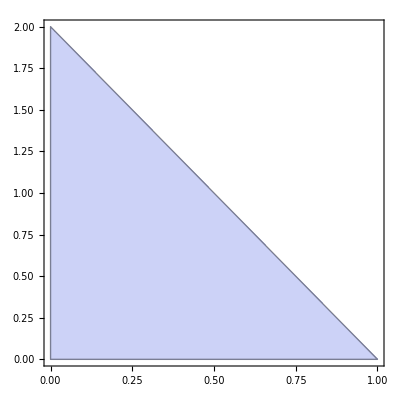

```mathematica
Block[{a=1,b=2},RegionPlot[ineq,{x,0,a},{y,0,b}]]
```

### Schematic Figure

```mathematica
right=Triangle[{{0,0},{b,0},{0,a}}];
```

```mathematica
r=right/.{a->1,b->1.5};
pts={v[[1]],C,v[[2]],A,v[[3]],B};

Show[Graphics[{r,
PerpSquare[Rest[Sides[r]],.05,4],
PointLabels[r,pts,.03,-.05]
},AspectRatio->Automatic]
]
```

⁃Graphics⁃

### Sangaku

```mathematica
Show[Graphics[RightTriangleSquares[8,{3,1.6}]],AspectRatio->Automatic,PlotRange->All]
```

⁃Graphics⁃

```mathematica
rr[3,{a,b}]^2-rr[1,{a,b}]rr[5,{a,b}]
```

0

## Distinct right triangles having identical areas

```mathematica
l1={{1380,19019,19069},{3059,8580,9109},{4485,5852,7373}};
```

```mathematica
RightQ[SidesToTriangle@@#]&/@l1
```

{True,True,True}

```mathematica
TriangleArea[Triangle[#]]&/@{{1380,19019,19069},{3059,8580,9109},{4485,5852,7373}}
```

{13123110,13123110,13123110}

```mathematica
l2={{24,70,74},{40,42,58},{15,112,113}};
```

```mathematica
RightQ[SidesToTriangle@@#]&/@l2
```

{True,True,True}

```mathematica
TriangleArea[Triangle[#]]&/@l2
```

{840,840,840}

## Properties

### Area

#### Area

```mathematica
Assuming[assum,FullSimplify[Area[reg]]]//Timing
```

{0.0017,(a b)/2}

```mathematica
Assuming[assum,FullSimplify[Area[implreg]]]//Timing
```

{0.15365,(a b)/2}

#### Formula

```mathematica
TriangleArea[right]
```

(a b)/2

#### Integrate

```mathematica
Assuming[a>0&&b>0,Area[ineq[x,y],{x,y}]]
```

(a b)/2

#### RegionMeasure

```mathematica
Assuming[assum,FullSimplify[RegionMeasure[reg]]]
```

(a b)/2

```mathematica
Assuming[assum,FullSimplify[RegionMeasure[implreg]]]
```

(a b)/2

### AreaInertiaTensor

```mathematica
Assuming[a>0&&b>0,AreaInertiaTensor[ineq[x,y],{x,y}]]
```

{{(a b^3)/12,-1/24 a^2 b^2},{-1/24 a^2 b^2,(a^3 b)/12}}

### Circumradius

```mathematica
FullSimplify[(ToSidelengths[Circumradius]/.Thread[{a,b,c}->abc]),𝒶>0&&𝒷>0]
```

1/2 √(𝒶^2+𝒷^2)

### Centroid

#### Integrate

```mathematica
Assuming[a>0&&b>0,Centroid[ineq[x,y],{x,y}]]
```

{a/3,b/3}

#### RegionCentroid

```mathematica
Assuming[assum,FullSimplify[RegionCentroid[reg]]]//Timing
```

{0.00156,{a/3,b/3}}

```mathematica
Assuming[assum,FullSimplify[RegionCentroid[implreg]]]//Timing
```

{0.02115,{a/3,b/3}}

### GeneralizedDiameter

```mathematica
ineqs=FullSimplify[And@@ineq@@@{{x1,y1},{x2,y2}},a>0&&b>0]
```

y1≥0&&a b≥b x1+a y1&&x1≥0&&y2≥0&&a b≥b x2+a y2&&x2≥0

```mathematica
Maximize[{(x1-x2)^2+(y1-y2)^2,ineqs},{x1,x2,y1,y2},Reals]//Timing
```

$Aborted

### Inradius

```mathematica
FullSimplify[(ToSidelengths[Inradius]/.Thread[{a,b,c}->abc]),𝒶>0&&𝒷>0]
```

```mathematica
(√((𝒶 𝒷 (𝒶+𝒷-√(𝒶^2+𝒷^2)))/(𝒶+𝒷+√(𝒶^2+𝒷^2))))/(√2)/.{𝒶->a,𝒷->b}
```

(√((a b (a+b-√(a^2+b^2)))/(a+b+√(a^2+b^2))))/(√2)

### RadiiOfGyration

```mathematica
Assuming[a>0&&b>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]
```

{b/(√6),a/(√6)}

## Inradius

```mathematica
r=right/.{a->1,b->1.5};
i=Incenter[r];
v=Vertices[r];

pts={v[[1]],C,v[[2]],A,v[[3]],B};
bluepts={i,"
StyleBox[\"I\",\nFontSlant->\"Italic\"]"};
Show[Graphics[{
r,
PerpSquare[Rest[Sides[r]],.05,4],
{Thickness[.01],Incircle[r]},
{
Red,
PerpSquare[#,.05,2]&/@Transpose[{PedalLines[r,i],Sides[r]}],Dashing[{.02,.02}],
PedalLines[r,i]
},
{
Blue,
PointLabels[r,bluepts,.03,.05],Line[{#[[1]],Coordinates@i,#[[2]]}]&/@Partition[Vertices[r],2,1,1]
},
PointLabels[r,pts,.03,-.05]
},AspectRatio->Automatic]
]
```

⁃Graphics⁃

```mathematica
i=PowerExpand[Inradius[right]]
```

(√(a+b-√(a^2+b^2)) √(a-b+√(a^2+b^2)) √(-a+b+√(a^2+b^2)))/(2 √(a+b+√(a^2+b^2)))

```mathematica
i/.Sqrt[a^2+b^2]:>c
```

(√(a+b-c) √(a-b+c) √(-a+b+c))/(2 √(a+b+c))

```mathematica
FullSimplify[i^2]
```

1/2 (a^2+a b+b^2-(a+b) √(a^2+b^2))

```mathematica
FullSimplify[(c^2+a b-(a+b)c)/2]
```

1/2 (a-c) (b-c)

```mathematica
FullSimplify[((c-a)(c-b)/2)-((a+b-c)/2)^2/.c->Sqrt[a^2+b^2]]
```

0

```mathematica
FullSimplify[((c-a)(c-b)/2)-(a b/(a+b+c))^2/.c->Sqrt[a^2+b^2]]
```

0

```mathematica
r[a_,b_]:=Module[{c=Sqrt[a^2+b^2]},
{Inradius[Triangle[{{0,0},{0,a},{b,0}}]],Sqrt[(c-a)(c-b)/2],(a+b-c)/2,a b/(a+b +c)}
]
```

```mathematica
{r[3,4],r[5,12],r[8,15],r[7,24]}//ColumnForm
```

{1,1,1,1}
{2,2,2,2}
{3,3,3,3}
{3,3,3,3}

## Circumradius

```mathematica
FullSimplify[PowerExpand[Circumradius[Triangle[{{0,0},{b,0},{0,a}}]]]]
```

(a b √(a^2+b^2))/(√(a+b-√(a^2+b^2)) √(a-b+√(a^2+b^2)) √(-a+b+√(a^2+b^2)) √(a+b+√(a^2+b^2)))

```mathematica
Sqrt[Simplify[%^2]]
```

1/2 √(a^2+b^2)

```mathematica
FullSimplify[a b c/Sqrt[(a+b+c)(b+c-a)(c+a-b)(a+b-c)]/.c->Sqrt[a^2+b^2]]
```

(a b √(a^2+b^2))/(2 √(a^2 b^2))

```mathematica
PowerExpand[%]
```

1/2 √(a^2+b^2)

## Median and Altitude

```mathematica
t=Triangle[5,4,3];
```

```mathematica
Show[Graphics[{
t,
{Blue,
AngleBisectors[t][[1]],
EqualAngleDivisionTicks[t,2,.4,.1,.4,VertexArcs->True][[1]]
},
{Green,Medians[t][[1]]},
{Red,Altitudes[t]},
PointLabels[Join[
Transpose[{VertexPoints[t],{"A","B","C"}}],
{
{Midpoints[t][[1]],"M_A", Green},
{Feet[Altitudes[t]][[1]],"H_A", Red},
{EndPoint[AngleBisectors[t][[1]]],"T_A",Blue}
}
],PointSize[.04],LabelOffset->-.2]
}],AspectRatio->Automatic,PlotRange->All]
```

⁃Graphics⁃